## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

```mathematica
numsamples=All; (*number of samples to take for error estimates. Set to "All" if not in debug-mode!*)
```

The following line sets up blocking during the creation of Jackknife samples with block size 1.

```mathematica
MakeJacknifeSamplesB[x_]:=MakeJacknifeSamples[x,1];
```

```mathematica
thisquarkchannel="u-d";
```

## Constants

```mathematica
scalingNat = .1973270524; (* this is GeV*fm *)
```

```mathematica
quarkchannelshort[quarkchannel_]:=Switch[quarkchannel,"up","U","down","D","u-d","UminusD",_,Message["INVALID QUARK CHANNEL"]];
```

```mathematica
basedatapath="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/

```mathematica
exportdatapath[quarkchannel_]:=basedatapath<>quarkchannelshort[quarkchannel]<>"_";
```

```mathematica
resamplingext="_"<>"jn";
```

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
platdb1=BIDATEXReader[exportdatapath[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
```

< -MemDB- {aBDBIndex,correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

```mathematica
MemDBGet[platdb1,MemDBSelect[platdb1,{numberFilter->Re}],sinkMom]//Union
```

{{-1,0,0}}

```mathematica
v1[v3_]:=v3*0.303;
vinterpolation[gammaValueI_,numberFilterI_, linkPathI_, eta_]:=
(
vlinks = Union[MemDBGet[platdb1,MemDBSelect[platdb1,{numberFilter->Re}],sideLink]];
vlinksv3 = Select[vlinks,Count[#,3]==eta&];
(*Print[vlinksv3];*)
vvectoranddata={};
Do[
v1data=PathToShift[vlinksv3[[i]],3];
correlatordata = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->gammaValueI,numberFilter->numberFilterI,linkPath->linkPathI,sideLink->vlinksv3[[i]]}],data];
AppendTo[vvectoranddata,{v1data,correlatordata[[1]]}]
,{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
(*Print[vvectoranddata//OutputForm];
Print[groupSamev//OutputForm];*)
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamev];
(*Print[averagedTableEvengPlusImForv//OutputForm];*)
dataforInterpolation ={};
v1dataforInterpolation ={};
Do[
AppendTo[v1dataforInterpolation,v1[averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];
,{i, Length[averagedTableEvengPlusImForv]}];
(*Print[Transpose[{v1dataforInterpolation,dataforInterpolation}]//OutputForm];*)
fninterpol = Interpolation[Transpose[{v1dataforInterpolation,dataforInterpolation}],InterpolationOrder->2];
Return[fninterpol[0]];
);
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 7]//OutputForm]
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 8]//OutputForm]
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 9]//OutputForm]
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 10]//OutputForm]
```

-6
⟨-360(740) × 10  ⟩_(2902J)

-6
⟨-830(730) × 10  ⟩_(2902J)

-6
⟨-930(650) × 10  ⟩_(2902J)

⟨-0.00137(60)⟩_(2902J)

{⟨-0.0019(23)⟩_(RowBox[{),⟨-0.0028(18)⟩_(RowBox[{),⟨-0.0031(14)⟩_(RowBox[{),⟨-0.0030(12)⟩_(RowBox[{),⟨-0.00244(92)⟩_(RowBox[{),⟨-0.00139(82)⟩_(RowBox[{),⟨-0.00104(76)⟩_(RowBox[{),⟨-170(680) × 10⟩_(RowBox[{),⟨-440(610) × 10⟩_(RowBox[{),⟨-770(590) × 10⟩_(RowBox[{)}

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

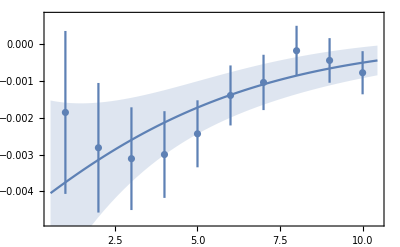
{fitSamples→{⟨0.6 ± 3.6⟩_(RowBox[{),{⟨-0.0044(31)⟩_(RowBox[{),⟨0.21(11)⟩_(RowBox[{)}},plot→-Graphics-,fitParameters→{A→ErrorBoundsRel[-0.00442708,0.00303726],B→ErrorBoundsRel[0.210714,0.105896]},chisqrPDOF→0.543269}

fitSamples -> {⟨0.6 ± 3.6⟩_(2902J), {⟨-0.0044(31)⟩_(2902J), ⟨0.21(11)⟩_(2902J)}}

{⟨0.6 ± 3.6⟩_(RowBox[{),{⟨-0.0044(31)⟩_(RowBox[{),⟨0.21(11)⟩_(RowBox[{)}}

⟨-0.0044(31)⟩_(RowBox[{)

⟨0.21(11)⟩_(RowBox[{)

```mathematica
xdata = {1,2,3,4,5,6,7,8,9,10};
ydata =Table[vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = etav], {etav, xdata}]
fit = ResamplingFit2D[xdata,ydata,A*Exp[-B*v],v,{A, B}]
Print[fit[[1]]//OutputForm]
fitpara = fitSamples/.fit
fitA= fitpara[[All,2]][[All,1]]
fitB= fitpara[[All,2]][[All,2]]
```

```mathematica
AllLinkPathList = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,numberFilter->Re}],linkPath];
Print[ "Total No. linkPath = ",Length[AllLinkPathList]]
Print[ "Total No. Distinct linkPath = ",CountDistinct[AllLinkPathList]]
DistinctLinkPaths= DeleteDuplicates[AllLinkPathList];
(*Do[Print[i,") ",PathToShift[DistinctLinkPaths[[i+1]],3],"<------->",DistinctLinkPaths[[i+1]], "<------->", MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->DistinctLinkPaths[[i+1]]}],sideNum]//DeleteDuplicates],{i,CountDistinct[AllLinkPathList]-1}]*)
Print["linkPaths -> {} are skipped"];
bveclinkPathsideNumLIST={};
Do[
AppendTo[bveclinkPathsideNumLIST,{PathToShift[DistinctLinkPaths[[i+1]],3],DistinctLinkPaths[[i+1]]}],{i,CountDistinct[AllLinkPathList]-1}]
(*bveclinkPathsideNumLIST//MatrixForm*)
bveclinkPathsideNumLISTforbL0=Select[bveclinkPathsideNumLIST,#[[1,1]]==0&];
bveclinkPathsideNumLISTforbLpositive=Select[bveclinkPathsideNumLIST,#[[1,1]]>0&];
bveclinkPathsideNumLISTforbLnegative=Select[bveclinkPathsideNumLIST,#[[1,1]]<0&];
b2list= Union[bveclinkPathsideNumLIST[[All,1]][[All,2]]];
b1list= Union[bveclinkPathsideNumLIST[[All,1]][[All,1]]];
Print["b2 = ",b2list]
Print["b1 = ",b1list]
bveclinkPathsideNumLISTforbL0//MatrixForm
bveclinkPathsideNumLISTforbLpositive//MatrixForm
bveclinkPathsideNumLISTforbLnegative//MatrixForm
bveclinkPathsideNumLISTforbL0//Length
bveclinkPathsideNumLISTforbLpositive//Length
bveclinkPathsideNumLISTforbLnegative//Length
noError=True;
Do[If[(bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]]+bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bveclinkPathsideNumLISTforbLpositive[",i, "]"];noError=False;],{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found "]];
```

Total No. linkPath = 7225

Total No. Distinct linkPath = 87

linkPaths -> {} are skipped

b2 = {-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}

b1 = {-8,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,8}

({0,1,0} | {2}
{0,2,0} | {2,2}
{0,3,0} | {2,2,2}
{0,4,0} | {2,2,2,2}
{0,5,0} | {2,2,2,2,2}
{0,6,0} | {2,2,2,2,2,2}
{0,7,0} | {2,2,2,2,2,2,2}
{0,-1,0} | {-2}
{0,-2,0} | {-2,-2}
{0,-3,0} | {-2,-2,-2}
{0,-4,0} | {-2,-2,-2,-2}
{0,-5,0} | {-2,-2,-2,-2,-2}
{0,-6,0} | {-2,-2,-2,-2,-2,-2}
{0,-7,0} | {-2,-2,-2,-2,-2,-2,-2})

({1,1,0} | {2,1}
{2,2,0} | {2,1,2,1}
{3,3,0} | {2,1,2,1,2,1}
{4,4,0} | {2,1,2,1,2,1,2,1}
{5,5,0} | {2,1,2,1,2,1,2,1,2,1}
{1,1,0} | {1,2}
{2,2,0} | {1,2,1,2}
{3,3,0} | {1,2,1,2,1,2}
{4,4,0} | {1,2,1,2,1,2,1,2}
{5,5,0} | {1,2,1,2,1,2,1,2,1,2}
{1,2,0} | {2,1,2}
{2,4,0} | {2,1,2,2,1,2}
{3,6,0} | {2,1,2,2,1,2,2,1,2}
{2,1,0} | {1,2,1}
{4,2,0} | {1,2,1,1,2,1}
{6,3,0} | {1,2,1,1,2,1,1,2,1}
{4,1,0} | {1,1,2,1,1}
{8,2,0} | {1,1,2,1,1,1,1,2,1,1}
{1,-1,0} | {-2,1}
{2,-2,0} | {-2,1,-2,1}
{3,-3,0} | {-2,1,-2,1,-2,1}
{4,-4,0} | {-2,1,-2,1,-2,1,-2,1}
{5,-5,0} | {-2,1,-2,1,-2,1,-2,1,-2,1}
{1,-1,0} | {1,-2}
{2,-2,0} | {1,-2,1,-2}
{3,-3,0} | {1,-2,1,-2,1,-2}
{4,-4,0} | {1,-2,1,-2,1,-2,1,-2}
{5,-5,0} | {1,-2,1,-2,1,-2,1,-2,1,-2}
{1,-2,0} | {-2,1,-2}
{2,-4,0} | {-2,1,-2,-2,1,-2}
{3,-6,0} | {-2,1,-2,-2,1,-2,-2,1,-2}
{2,-1,0} | {1,-2,1}
{4,-2,0} | {1,-2,1,1,-2,1}
{6,-3,0} | {1,-2,1,1,-2,1,1,-2,1}
{4,-1,0} | {1,1,-2,1,1}
{8,-2,0} | {1,1,-2,1,1,1,1,-2,1,1})

({-1,1,0} | {2,-1}
{-2,2,0} | {2,-1,2,-1}
{-3,3,0} | {2,-1,2,-1,2,-1}
{-4,4,0} | {2,-1,2,-1,2,-1,2,-1}
{-5,5,0} | {2,-1,2,-1,2,-1,2,-1,2,-1}
{-1,1,0} | {-1,2}
{-2,2,0} | {-1,2,-1,2}
{-3,3,0} | {-1,2,-1,2,-1,2}
{-4,4,0} | {-1,2,-1,2,-1,2,-1,2}
{-5,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2}
{-1,2,0} | {2,-1,2}
{-2,4,0} | {2,-1,2,2,-1,2}
{-3,6,0} | {2,-1,2,2,-1,2,2,-1,2}
{-2,1,0} | {-1,2,-1}
{-4,2,0} | {-1,2,-1,-1,2,-1}
{-6,3,0} | {-1,2,-1,-1,2,-1,-1,2,-1}
{-4,1,0} | {-1,-1,2,-1,-1}
{-8,2,0} | {-1,-1,2,-1,-1,-1,-1,2,-1,-1}
{-1,-1,0} | {-2,-1}
{-2,-2,0} | {-2,-1,-2,-1}
{-3,-3,0} | {-2,-1,-2,-1,-2,-1}
{-4,-4,0} | {-2,-1,-2,-1,-2,-1,-2,-1}
{-5,-5,0} | {-2,-1,-2,-1,-2,-1,-2,-1,-2,-1}
{-1,-1,0} | {-1,-2}
{-2,-2,0} | {-1,-2,-1,-2}
{-3,-3,0} | {-1,-2,-1,-2,-1,-2}
{-4,-4,0} | {-1,-2,-1,-2,-1,-2,-1,-2}
{-5,-5,0} | {-1,-2,-1,-2,-1,-2,-1,-2,-1,-2}
{-1,-2,0} | {-2,-1,-2}
{-2,-4,0} | {-2,-1,-2,-2,-1,-2}
{-3,-6,0} | {-2,-1,-2,-2,-1,-2,-2,-1,-2}
{-2,-1,0} | {-1,-2,-1}
{-4,-2,0} | {-1,-2,-1,-1,-2,-1}
{-6,-3,0} | {-1,-2,-1,-1,-2,-1,-1,-2,-1}
{-4,-1,0} | {-1,-1,-2,-1,-1}
{-8,-2,0} | {-1,-1,-2,-1,-1,-1,-1,-2,-1,-1})

14

36

36

✓ Checked: linkPaths corresponding to   are found

```mathematica
GiveTablePlateauEvengPlusImForb[etavalue_]:=(
(*Print["\n eta PlateauRange = ", PlateauRange, "\n"];
Print["Forming A12b"]*)
PlateauRange=etavalue;
a=0.114;
S3=1;
modP1=339.3;
P0=Sqrt[(1067^2)+(339.3^2)];
latticemodP1=1;
latticeP0=(P0*a)/197;
Pplus=(latticemodP1+latticeP0)/Sqrt[2];
MN=(1067*a)/197;
TablePlateauEvengPlusImForb = {};
(*Print["considering only positive b2"];*)
Do[
If[ bveclinkPathsideNumLISTforbL0[[i,1]][[2]]<0,Continue[]];
bl0g8Im = vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g1Re = vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g3Re = vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
b2valuebL0= bveclinkPathsideNumLISTforbL0[[i,1]][[2]];

bl0A12B = ((1/(2*M*S3*b2valuebL0*Pplus))*((-bl0g1Re/Sqrt[2])-(bl0g8Im/Sqrt[2])-(((P1-P0)*bl0g3Re)/(v1BYv3*P0))));

AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbL0[[i,1]],bl0A12BPplus}];
  ,{i,Length[bveclinkPathsideNumLISTforbL0]}];

Do[
If[ bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]]<0,Continue[]];

blPg8Im = vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg1Re = vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg2Re = vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg3Re = vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];

b2valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]];
b1valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]];

blNg8Im=vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg1Re=vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg2Re=vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg3Re=vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];

b2valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[2]];
b1valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]];

blPA12B=-((1/(Sqrt[2]*2*Pplus*b2valuebLP*M*S3))*(blPg8Im+(P1*blPg3Re/v1BYv3*P0)))-((b2valuebLP/(Sqrt[2]*2*Pplus*(b2valuebLP*b2valuebLP+b1valuebLP*b1valuebLP)*M*S3))*(blPg1Re+(b1valuebLP*blPg2Re/b2valuebLP)-((b2valuebLP*b2valuebLP-b1valuebLP*b1valuebLP)*blPg3Re/v1BYv3*b2valuebLP*b2valuebLP)));

blNA12B=-((1/(Sqrt[2]*2*Pplus*b2valuebLN*M*S3))*(blNg8Im+(P1*blNg3Re/v1BYv3*P0)))-((b2valuebLN/(Sqrt[2]*2*Pplus*(b2valuebLN*b2valuebLN+b1valuebLN*b1valuebLN)*M*S3))*(blNg1Re+(b1valuebLN*blNg2Re/b2valuebLN)-((b2valuebLN*b2valuebLN-b1valuebLN*b1valuebLN)*blNg3Re/v1BYv3*b2valuebLN*b2valuebLN)));
blEvengPlusImEta = (blPA12BPplus+blNA12BPplus)/2;

AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbLpositive[[i,1]],blEvengPlusImEta}];
AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbLnegative[[i,1]],blEvengPlusImEta}];
  ,{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
Return[TablePlateauEvengPlusImForb];
)
```

```mathematica
PlotA12B[etavalue_]:=(
TablePlateauEvengPlusImForb = GiveTablePlateauEvengPlusImForb[etavalue];
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTablePlateauEvengPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Print["\n etavalue = ", etavalue];
(*Print["✓ Same  with different linkPath are averaged\n"];*)
bTlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,2]]];
bLlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,1]]];
PlotbLforDiffbTList={};
Do[
PlotbL2=Transpose[{Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTList,PlotbL2];
 ,{bT,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Return[Print[PlotbL]];
)
```

```mathematica
PlotA12B[8]
```

etavalue = 8

ResamplingStatistics::nimp: Symbol-Statistics not implemented

$Aborted

```mathematica
baveragedTableA12B[etavalue_]:=(
TablePlateauEvengPlusImForb = GiveTablePlateauEvengPlusImForb[etavalue];
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTableA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Return[averagedTableA12B];
)
baveragedTableA12BforeachbT[etavalue_, bT_]:=(
TablePlateauEvengPlusImForb = GiveTablePlateauEvengPlusImForb[etavalue];
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTableA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
averagedTableA12BforeachbT=Transpose[{Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
Return[averagedTableA12BforeachbT];
)
Print["bT = 1 & eta = 7"]
Print[baveragedTableA12BforeachbT[7,1][[1]][[2]]//OutputForm]
Print[baveragedTableA12BforeachbT[7,1][[1]][[2]]//FullForm]
```

bT = 1 & eta = 7

bl0A12BPplus

bl0A12BPplus

```mathematica
etalist = {6,7,8,9,10}
etabA12B =Table[baveragedTableA12B[etaVlue], {etaVlue, etalist}]
```

{6,7,8,9,10}

{{{{0,1,0},bl0A12BPplus},{{0,2,0},bl0A12BPplus},{{0,3,0},bl0A12BPplus},{{0,4,0},bl0A12BPplus},{{0,5,0},bl0A12BPplus},{{0,6,0},bl0A12BPplus},{{0,7,0},bl0A12BPplus},{{1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{-5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{8,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-8,2,0},(blNA12BPplus+blPA12BPplus)/2}},{{{0,1,0},bl0A12BPplus},{{0,2,0},bl0A12BPplus},{{0,3,0},bl0A12BPplus},{{0,4,0},bl0A12BPplus},{{0,5,0},bl0A12BPplus},{{0,6,0},bl0A12BPplus},{{0,7,0},bl0A12BPplus},{{1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{-5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{8,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-8,2,0},(blNA12BPplus+blPA12BPplus)/2}},{{{0,1,0},bl0A12BPplus},{{0,2,0},bl0A12BPplus},{{0,3,0},bl0A12BPplus},{{0,4,0},bl0A12BPplus},{{0,5,0},bl0A12BPplus},{{0,6,0},bl0A12BPplus},{{0,7,0},bl0A12BPplus},{{1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{-5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{8,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-8,2,0},(blNA12BPplus+blPA12BPplus)/2}},{{{0,1,0},bl0A12BPplus},{{0,2,0},bl0A12BPplus},{{0,3,0},bl0A12BPplus},{{0,4,0},bl0A12BPplus},{{0,5,0},bl0A12BPplus},{{0,6,0},bl0A12BPplus},{{0,7,0},bl0A12BPplus},{{1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{-5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{8,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-8,2,0},(blNA12BPplus+blPA12BPplus)/2}},{{{0,1,0},bl0A12BPplus},{{0,2,0},bl0A12BPplus},{{0,3,0},bl0A12BPplus},{{0,4,0},bl0A12BPplus},{{0,5,0},bl0A12BPplus},{{0,6,0},bl0A12BPplus},{{0,7,0},bl0A12BPplus},{{1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,1,0},(blNA12BPplus+blPA12BPplus)/2},{{2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,2,0},(blNA12BPplus+blPA12BPplus)/2},{{3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,4,0},(blNA12BPplus+blPA12BPplus)/2},{{5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{-5,5,0},(blNA12BPplus+blPA12BPplus)/2},{{1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-1,2,0},(blNA12BPplus+blPA12BPplus)/2},{{2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,4,0},(blNA12BPplus+blPA12BPplus)/2},{{3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{-3,6,0},(blNA12BPplus+blPA12BPplus)/2},{{2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-2,1,0},(blNA12BPplus+blPA12BPplus)/2},{{4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,2,0},(blNA12BPplus+blPA12BPplus)/2},{{6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{-6,3,0},(blNA12BPplus+blPA12BPplus)/2},{{4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{-4,1,0},(blNA12BPplus+blPA12BPplus)/2},{{8,2,0},(blNA12BPplus+blPA12BPplus)/2},{{-8,2,0},(blNA12BPplus+blPA12BPplus)/2}}}

```mathematica
etafitAofA12B = {};
etafitBofA12B = {};
Do[
foreachb = {};
Do[
AppendTo[foreachb, etabA12B[[i]][[b]][[2]]];
,{i,Length[etabA12B]}];
fit1 = ResamplingFit2D[etalist,foreachb,A*Exp[-B*v],v,{A, B}];
fitpara1 = fitSamples/.fit1;
fitA1= fitpara1[[All,2]][[All,1]];
fitB1= fitpara1[[All,2]][[All,2]];
AppendTo[etafitAofA12B,{etabA12B[[1]][[b]][[1]],fitA1}];
AppendTo[etafitBofA12B,{etabA12B[[1]][[b]][[1]],fitB1}];
,{b,Length[etabA12B[[1]]]}];
etafitAofA12B
etafitBofA12B
```

ResamplingStatistics::nimp: Symbol-Statistics not implemented

$Aborted

{}

{}

```mathematica
newetafitAofA12B= Select[etafitAofA12B,#[[1]]!={4,1,0}&&#[[1]]!={-4,1,0}&];
newetafitBofA12B= Select[etafitBofA12B,#[[1]]!={4,1,0}&&#[[1]]!={-4,1,0}&];

bTlist= Union[newetafitAofA12B[[All,1]][[All,2]]];
bLlist= Union[newetafitAofA12B[[All,1]][[All,1]]];
PlotbLforDiffbTListforA={};
Do[
PlotbLforAi=Transpose[{Select[newetafitAofA12B, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[newetafitAofA12B, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTListforA,PlotbLforAi];
 ,{bT,bTlist}];
PlotbLforA= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTListforA[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Print["A"];
Print[PlotbLforA];
PlotbLforDiffbTListforB={};
Do[
PlotbLforBi=Transpose[{Select[newetafitBofA12B, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[newetafitBofA12B, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTListforB,PlotbLforBi];
 ,{bT,bTlist}];
PlotbLforB= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTListforB[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Print["B"];
Print[PlotbLforB];
```

A

-Graphics-

B

-Graphics-

```mathematica
(*datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,4,9,16,25};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print[" = ",bsquarelist]
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];*)
```